# In Class Demo - 3 May 2024

## Finding the Center Manifold

Enter the system defined by the system of differential equation given by ,

```mathematica
f[x_,y_] = x y - x +y;
g[x_,y_] = x - x^2- y;
eqPt=Solve[{f[x,y]==0,g[x,y]==0},{x,y}]
```

{{x→0,y→0}}

Now, let’s approximate the invariant center manifold with a function of the form y = h(x) where we will write  as a Taylor Polynomial of the form

```mathematica
h[x_] = Sum[Subscript[a, j] x^j,{j,0,5}]
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5

The requirements for the center manifold are threefold:

The manifold must go through the equilibrium point (If , then )

The manifold must be tangent to the eigenvector corresponding to .  That is,

The manifold must be invariant.  That means, for any trajectory starting on the curve, it must remain on the curve for all time (forwards and backwards).  That means that if , then  where  and  are restricted to the manifold such that This is telling us that the flow is pushing solutions along the manifold.

In what follows, let’s start with the following equation:  which can be written as .  Since we want to restrict this to the manifold, we have  which can be expressed as follows:

```mathematica
eqn = g[x,h[x]]- D[h[x],x]f[x,h[x]];
Expand[eqn]
```

x-x^2-a_0-a_0 a_1-x a_0 a_1-x a_1^2-x^2 a_1^2+x^2 a_2-2 x a_0 a_2-2 x^2 a_0 a_2-3 x^2 a_1 a_2-3 x^3 a_1 a_2-2 x^3 a_2^2-2 x^4 a_2^2+2 x^3 a_3-3 x^2 a_0 a_3-3 x^3 a_0 a_3-4 x^3 a_1 a_3-4 x^4 a_1 a_3-5 x^4 a_2 a_3-5 x^5 a_2 a_3-3 x^5 a_3^2-3 x^6 a_3^2+3 x^4 a_4-4 x^3 a_0 a_4-4 x^4 a_0 a_4-5 x^4 a_1 a_4-5 x^5 a_1 a_4-6 x^5 a_2 a_4-6 x^6 a_2 a_4-7 x^6 a_3 a_4-7 x^7 a_3 a_4-4 x^7 a_4^2-4 x^8 a_4^2+4 x^5 a_5-5 x^4 a_0 a_5-5 x^5 a_0 a_5-6 x^5 a_1 a_5-6 x^6 a_1 a_5-7 x^6 a_2 a_5-7 x^7 a_2 a_5-8 x^7 a_3 a_5-8 x^8 a_3 a_5-9 x^8 a_4 a_5-9 x^9 a_4 a_5-5 x^9 a_5^2-5 x^10 a_5^2

Now, let’s collect each power of x^n using the CoefficientList command as follows:

```mathematica
coeffs=CoefficientList[Expand[eqn],x]
```

{-a_0-a_0 a_1,1-a_0 a_1-a_1^2-2 a_0 a_2,-1-a_1^2+a_2-2 a_0 a_2-3 a_1 a_2-3 a_0 a_3,-3 a_1 a_2-2 a_2^2+2 a_3-3 a_0 a_3-4 a_1 a_3-4 a_0 a_4,-2 a_2^2-4 a_1 a_3-5 a_2 a_3+3 a_4-4 a_0 a_4-5 a_1 a_4-5 a_0 a_5,-5 a_2 a_3-3 a_3^2-5 a_1 a_4-6 a_2 a_4+4 a_5-5 a_0 a_5-6 a_1 a_5,-3 a_3^2-6 a_2 a_4-7 a_3 a_4-6 a_1 a_5-7 a_2 a_5,-7 a_3 a_4-4 a_4^2-7 a_2 a_5-8 a_3 a_5,-4 a_4^2-8 a_3 a_5-9 a_4 a_5,-9 a_4 a_5-5 a_5^2,-5 a_5^2}

```mathematica
rules = {}
```

{}

### Leading Order:

```mathematica
coeffs[[1]]
rules = Flatten[{rules,Solve[coeffs[[1]]==0,Subscript[a, 0]]}]
```

-a_0-a_0 a_1

{a_0→0}

### Next Order:

```mathematica
coeffs[[2]]/.rules
Solve[%==0,Subscript[a, 1]]
```

1-a_1^2

{{a_1→-1},{a_1→1}}

```mathematica
rules=Flatten[{rules,Subscript[a, 1]->1}]
```

{a_0→0,a_1→1}

### Next Order:

```mathematica
coeffs[[3]]/.rules
Solve[%==0,Subscript[a, 2]]
rules = Flatten[{rules,%}]
```

-2-2 a_2

{{a_2→-1}}

{a_0→0,a_1→1,a_2→-1}

### Next Order:

```mathematica
coeffs[[4]]/.rules
Solve[%==0,Subscript[a, 3]]
rules = Flatten[{rules,%}]
```

1-2 a_3

{{a_3→1/2}}

{a_0→0,a_1→1,a_2→-1,a_3→1/2}

### Next Order:

```mathematica
coeffs[[5]]/.rules
Solve[%==0,Subscript[a, 4]]
rules = Flatten[{rules,%}]
```

-3/2-2 a_4

{{a_4→-3/4}}

{a_0→0,a_1→1,a_2→-1,a_3→1/2,a_4→-3/4}

### Truncate

```mathematica
rules = Flatten[{rules,Subscript[a, 5]->0}]
```

{a_0→0,a_1→1,a_2→-1,a_3→1/2,a_4→-3/4,a_5→0}

```mathematica
h[x]/.rules
```

x-x^2+x^3/2-(3 x^4)/4

## Dynamics on the center manifold

Since we have , then to determine the dynamics on the center manifold, we need to look at the differential equation .  This will be a differential equation in  only and can be analyzed via the phaseline.  To see this, we have the following:

-1/4 x^3 (2+x+3 x^2)

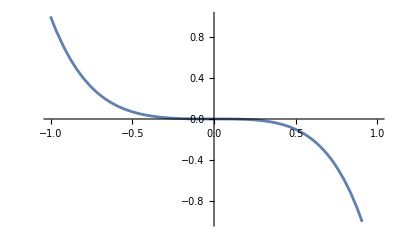

```mathematica
f[x,h[x]]/.rules//Simplify
Plot[f[x,h[x]/.rules],{x,-1,1}]
```

Note that the equilibrium point at x = 0 is stable based on the system  
Thus, the dynamic on the center manifold curve  are all traveling towards the origin!  We can see this in the plot of the original phase plane.

## Plotting the Center Manifold and the StreamPlot

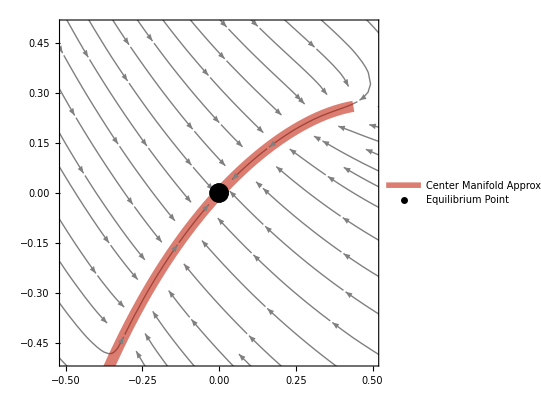

```mathematica
p1=StreamPlot[{f[x,y],g[x,y]},{x,-1,1},{y,-1,1},
StreamColorFunction->None,
StreamStyle->Gray,
StreamPoints->60,
StreamScale->Large];
p2=Plot[{h[x]/.rules},{x,-1/2,7/16},
PlotStyle->{
{
ColorData["SolarColors"][.2],
Thickness[.02],
Opacity[.56]
}
},
PlotLegends->{
"Center Manifold Approximation"
}];
p3 = ListPlot[{{0,0}},
PlotStyle->{Black,PointSize[.035]},
PlotLegends->{"   Equilibrium Point"}];
p4 = ContourPlot[{f[x,y]==0,g[x,y]==0},{x,-1,1},{y,-1,1},PlotLegends->{{" nullcline"," nullcline"}}];
Show[p1,p2,p3,PlotRange->{{-.5,.5},{-.5,.5}}]
```